```mathematica
SetDirectory[NotebookDirectory[]];
colors={RGBColor[0.863, 0.133, 0.196],RGBColor[0.17600000000000002, 0.41600000000000004, 0.631],RGBColor[0.9690000000000001, 0.6859999999999999, 0.20800000000000002],RGBColor[0.349, Rational[7, 10], 0.33299999999999996],RGBColor[1, 0.5, 0],RGBColor[0.557, 0.573, 0.569]};
GetColor[deg_]:=Module[{},
Which[
deg ==1, colors⟦1⟧,
deg==2,colors⟦2⟧,
deg==3, colors⟦3⟧,
True, colors⟦6⟧
]
]
TicksL =Table[{i,ToString[NumberForm[N[1-i/71],{3,1}]]},{i,Range[0,71,71/5]}];
```

# Load Data

```mathematica
SS = Import["data_FigS8/NetStructure/SSall.mx"];
Deg = Import["data_FigS8/NetStructure/Degree.mx"];
n= "0.3100000000000001_13.csv";
m23 = Transpose@Import["data_FigS10S11S12/M_SD_002_mean_3_"<>n,"Table"];
m25 = Transpose@Import["data_FigS10S11S12/M_SD_002_mean_5_"<>n,"Table"];
m215 = Transpose@Import["data_FigS10S11S12/M_SD_002_mean_15_"<>n,"Table"];
m275 = Transpose@Import["data_FigS10S11S12/M_SD_002_mean_75_"<>n,"Table"];
m2375 = Transpose@Import["data_FigS10S11S12/M_SD_002_mean_375_"<>n,"Table"];
vch23 = Transpose@Import["data_FigS10S11S12/M_SD_002_varCh_3_"<>n,"Table"];
vch25 =Transpose@ Import["data_FigS10S11S12/M_SD_002_varCh_5_"<>n,"Table"];
vch215 =Transpose@ Import["data_FigS10S11S12/M_SD_002_varCh_15_"<>n,"Table"];
vch275 =Transpose@ Import["data_FigS10S11S12/M_SD_002_varCh_75_"<>n,"Table"];
vch2375 =Transpose@ Import["data_FigS10S11S12/M_SD_002_varCh_375_"<>n,"Table"];
```

```mathematica
n= "0.4100000000000002_12.csv";
m93 = Transpose@Import["data_FigS10S11S12/M_SD_009_mean_3_"<>n,"Table"];
m95 = Transpose@Import["data_FigS10S11S12/M_SD_009_mean_5_"<>n,"Table"];
m915 = Transpose@Import["data_FigS10S11S12/M_SD_009_mean_15_"<>n,"Table"];
m975 = Transpose@Import["data_FigS10S11S12/M_SD_009_mean_75_"<>n,"Table"];
m9375 = Transpose@Import["data_FigS10S11S12/M_SD_009_mean_375_"<>n,"Table"];
vch93 = Transpose@Import["data_FigS10S11S12/M_SD_009_varCh_3_"<>n,"Table"];
vch95 =Transpose@ Import["data_FigS10S11S12/M_SD_009_varCh_5_"<>n,"Table"];
vch915 =Transpose@ Import["data_FigS10S11S12/M_SD_009_varCh_15_"<>n,"Table"];
vch975 =Transpose@ Import["data_FigS10S11S12/M_SD_009_varCh_75_"<>n,"Table"];
vch9375 =Transpose@ Import["data_FigS10S11S12/M_SD_009_varCh_375_"<>n,"Table"];m93750 = Table[Append[m9375⟦i⟧,0],{i,Length@m9375}];
m9 = {m93,m95,m915,m975,m93750};
v9={vch93,vch95,vch915,vch975,vch9375};
```

```mathematica
n= "0.4300000000000002_9.csv";
m113 = Transpose@Import["data_FigS10S11S12/M_SD_011_mean_3_"<>n,"Table"];
m115 = Transpose@Import["data_FigS10S11S12/M_SD_011_mean_5_"<>n,"Table"];
m1115 = Transpose@Import["data_FigS10S11S12/M_SD_011_mean_15_"<>n,"Table"];
m1175 = Transpose@Import["data_FigS10S11S12/M_SD_011_mean_75_"<>n,"Table"];
m11375 = Transpose@Import["data_FigS10S11S12/M_SD_011_mean_375_"<>n,"Table"];
vch113 = Transpose@Import["data_FigS10S11S12/M_SD_011_varCh_3_"<>n,"Table"];
vch115 =Transpose@ Import["data_FigS10S11S12/M_SD_011_varCh_5_"<>n,"Table"];
vch1115 =Transpose@ Import["data_FigS10S11S12/M_SD_011_varCh_15_"<>n,"Table"];
vch1175 =Transpose@ Import["data_FigS10S11S12/M_SD_011_varCh_75_"<>n,"Table"];
vch11375 =Transpose@ Import["data_FigS10S11S12/M_SD_011_varCh_375_"<>n,"Table"];m113750 = Table[Append[m11375⟦i⟧,0],{i,Length@m11375}];
m11 = {m113,m115,m1115,m1175,m113750};
v11={vch113,vch115,vch1115,vch1175,vch11375};
```

# MSD002 Mount Missim

## data

```mathematica
ews= Transpose@Import["data_FigS10S11S12/MSD02_EWSmean_.csv","Table"];
die= Transpose@Import["data_FigS10S11S12/M_SD_002_die_13.csv","Table"];
maxdie=Table[Max@die⟦i⟧,{i,5}];
m23750 = Table[Append[m2375⟦i⟧,0],{i,Length@m2375}];
m2 = {m23,m25,m215,m275,m23750};
v2={vch23,vch25,vch215,vch275,vch2375};
```

## make plots

### mean abundance

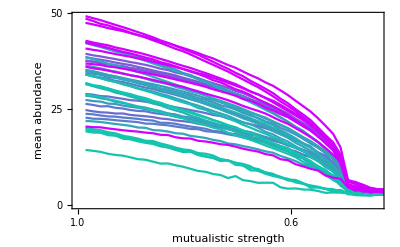
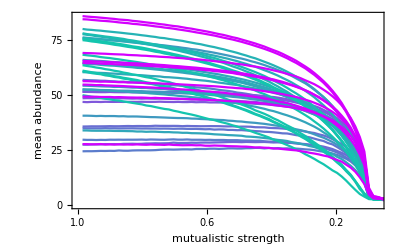
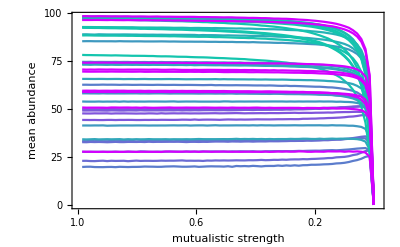

```mathematica
network = 2;
SensorScore=SS⟦network⟧;
vertexColors=(Blend[{ RGBColor[0.8300000000000001, 0, 1],RGBColor[0, 0.85, 0.65]},Rescale[#,{0,1}]]&)[#]&/@SensorScore;
meanpl=Table[
ListPlot[m2⟦i⟧,
Joined->True,
Frame->True,
PlotStyle->Partition[vertexColors,1],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
PlotRange->{{0,maxdie⟦i⟧+2},Automatic},
FrameTicksStyle->11,
FrameTicks->{{Range[0,100,25],None} ,{TicksL,None}},
FrameLabel->{"mutualistic strength","mean abundance",""}
],{i,{1,3,5}}]
```

### variance change

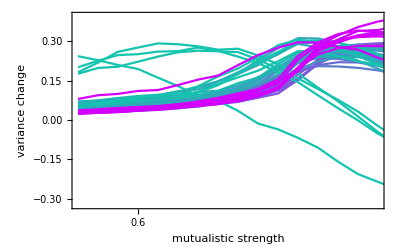
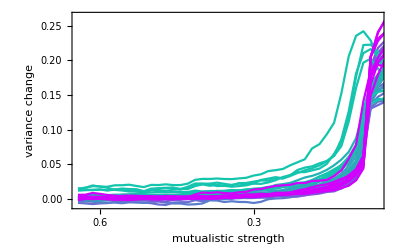
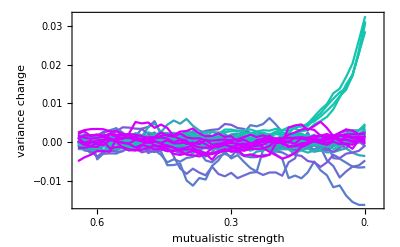

```mathematica
mu2 =N[Range[1,0,-1/Length[Transpose[m23]]]⟦-Length[Transpose[vch23]];;-1⟧];
1-(maxdie⟦1⟧+2)/70;
datach = Table[Table[Transpose@{mu2,v2⟦i⟧⟦j⟧},{j,Length@v2⟦1⟧}],{i,5}];
vchpl=Table[ListPlot[datach⟦i⟧,
Joined->True,
Frame->True,
PlotStyle->Partition[vertexColors,1],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
PlotRange->{{Max@mu2,1-(maxdie⟦i⟧+2)/70},Full},
PlotRange->Full,
FrameTicksStyle->11,
FrameTicks->{Automatic ,{Range[0,1,0.15],None}},
FrameLabel->{"mutualistic strength","variance change",""},
ScalingFunctions->{"Reverse",None}
],{i,{1,3,5}}]
```

### Sensor score vs early - warning score

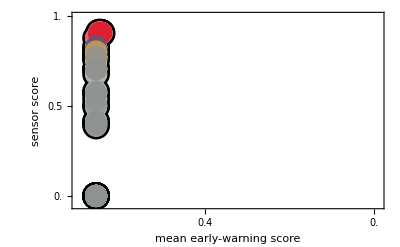
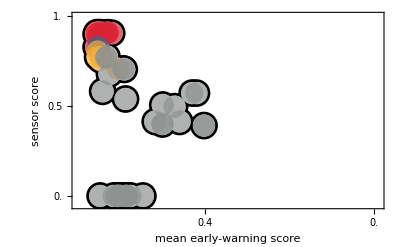
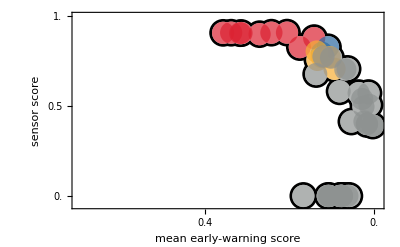

```mathematica
network = 2;

figs2=Table[

SensorScore = SS⟦network⟧;
vertexDegree=Deg⟦network⟧;
medianEW = ews⟦repetition⟧//Flatten;

n = Length@SensorScore;

degrees = Sort@DeleteDuplicates@vertexDegree;
deg = degrees⟦1⟧;

temp=Table[
pos = Position[vertexDegree,deg]//Flatten;

ListPlot[Thread[{medianEW⟦pos⟧, SensorScore⟦pos⟧}],
PlotRange->{{0-0.01,Max@medianEW+0.01},{-0.05,1}},
GridLines->{{},{Max@SensorScore}},
GridLinesStyle->Directive[Gray,Dashed],
PlotStyle->Directive[GetColor[deg], PointSize[0.04],Opacity[0.7]],
 FrameTicks->{{Range[0,1,0.2],None},{Range[0,Max@medianEW,0.05],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True
]
,{deg,degrees}];

temp2 = ListPlot[Thread[{medianEW, SensorScore}],
PlotRange->{{0-0.01,0.7},{-0.05,1}},
(*GridLines->{{},{Max@SensorScore}},*)
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
FrameTicks->{{Range[0,1,0.5],None},{Range[0,1,0.2],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True,
PlotStyle-> Directive[Black, PointSize[0.05],Opacity[1]],
FrameTicksStyle->11,
FrameLabel->{"mean early-warning score","sensor score",""}
];

temp3 = ListPlot[Thread[{medianEW, SensorScore}],
ScalingFunctions->{"Reverse",Identity},
PlotStyle-> Directive[White, PointSize[0.04],Opacity[1]]
];

Show[temp2,temp3,temp,
FrameTicksStyle->11
]
,{repetition,Range[3]}]
```

# MSD009

## data

```mathematica
ews= Transpose@Import["data_FigS10S11S12/MSD09_EWSmean_.csv","Table"];
die= Transpose@Import["data_FigS10S11S12/M_SD_009_die_12.csv","Table"];
```

## make plots

### mean abundance

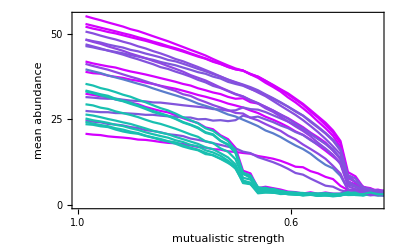
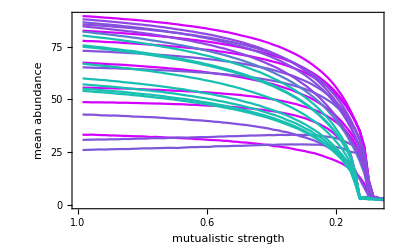
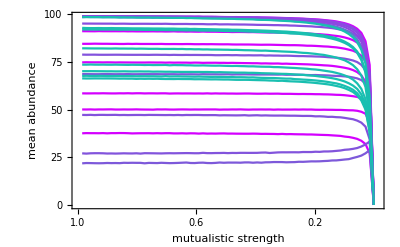

```mathematica
network = 5;
SensorScore=SS⟦network⟧;
vertexColors=(Blend[{ RGBColor[0.8300000000000001, 0, 1],RGBColor[0, 0.85, 0.65]},Rescale[#,{0,1}]]&)[#]&/@SensorScore;
meanpl=Table[
ListPlot[m9⟦i⟧,
Joined->True,
Frame->True,
PlotStyle->Partition[vertexColors,1],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
PlotRange->{{0,maxdie⟦i⟧+2},Automatic},
FrameTicksStyle->11,
FrameTicks->{{Range[0,100,25],None} ,{TicksL,None}},
FrameLabel->{"mutualistic strength","mean abundance",""}
],{i,{1,3,5}}]
```

### variance change

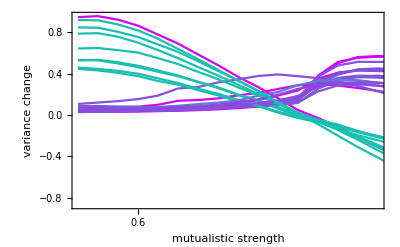
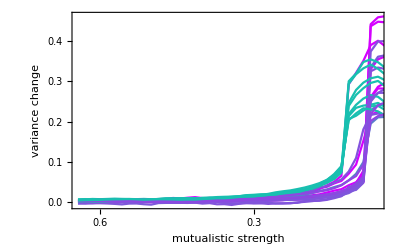
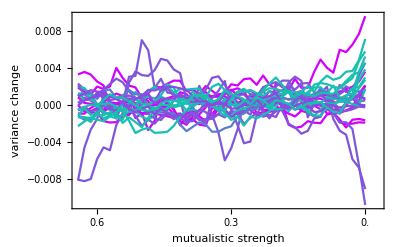

```mathematica
mu9 =N[Range[1,0,-1/Length[Transpose[m93]]]⟦-Length[Transpose[vch93]];;-1⟧];
1-(maxdie⟦1⟧+2)/70;
datCh = Table[Table[Transpose@{mu9,v9⟦i⟧⟦j⟧},{j,Length@v9⟦1⟧}],{i,5}];
vchpl=Table[ListPlot[datCh⟦i⟧,
Joined->True,
Frame->True,
PlotStyle->Partition[vertexColors,1],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
PlotRange->{{Max@mu2,1-(maxdie⟦i⟧+2)/70},Full},
PlotRange->Full,
FrameTicksStyle->11,
FrameTicks->{Automatic ,{Range[0,1,0.15],None}},
FrameLabel->{"mutualistic strength","variance change",""},
ScalingFunctions->{"Reverse",None}
],{i,{1,3,5}}]
```

### Sensor score vs early - warning score

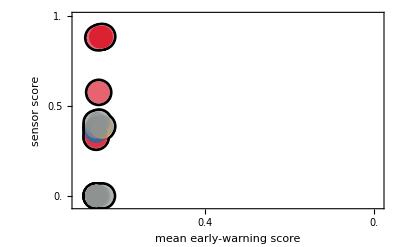
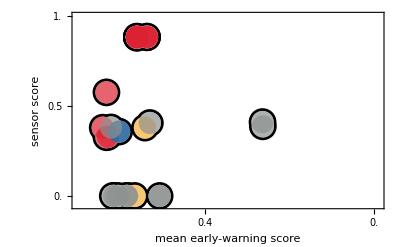
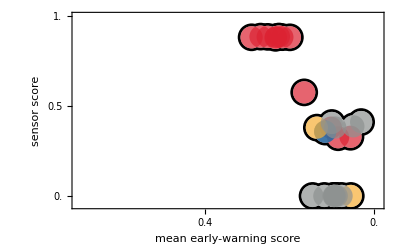

```mathematica
network = 5;

figs2=Table[

SensorScore = SS⟦network⟧;
vertexDegree=Deg⟦network⟧;
medianEW = ews⟦repetition⟧//Flatten;

n = Length@SensorScore;

degrees = Sort@DeleteDuplicates@vertexDegree;
deg = degrees⟦1⟧;

temp=Table[
pos = Position[vertexDegree,deg]//Flatten;

ListPlot[Thread[{medianEW⟦pos⟧, SensorScore⟦pos⟧}],
PlotRange->{{0-0.01,Max@medianEW+0.01},{-0.05,1}},
GridLines->{{},{Max@SensorScore}},
GridLinesStyle->Directive[Gray,Dashed],
PlotStyle->Directive[GetColor[deg], PointSize[0.04],Opacity[0.7]],
 FrameTicks->{{Range[0,1,0.2],None},{Range[0,Max@medianEW,0.05],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True
]
,{deg,degrees}];

temp2 = ListPlot[Thread[{medianEW, SensorScore}],
PlotRange->{{0-0.01,0.7},{-0.05,1}},
(*GridLines->{{},{Max@SensorScore}},*)
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
FrameTicks->{{Range[0,1,0.5],None},{Range[0,1,0.2],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True,
PlotStyle-> Directive[Black, PointSize[0.05],Opacity[1]],
FrameTicksStyle->11,
FrameLabel->{"mean early-warning score","sensor score",""}
];

temp3 = ListPlot[Thread[{medianEW, SensorScore}],
ScalingFunctions->{"Reverse",Identity},
PlotStyle-> Directive[White, PointSize[0.04],Opacity[1]]
];

Show[temp2,temp3,temp,
FrameTicksStyle->11
]
,{repetition,Range[3]}]
```

# MSD11

## data

```mathematica
ews= Transpose@Import["data_FigS10S11S12/MSD011_EWSmean_.csv","Table"];
die= Transpose@Import["data_FigS10S11S12/M_SD_011_die_9.csv","Table"];
```

## make plots

### mean abundance

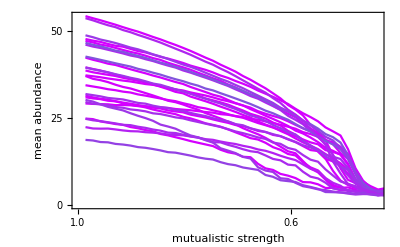
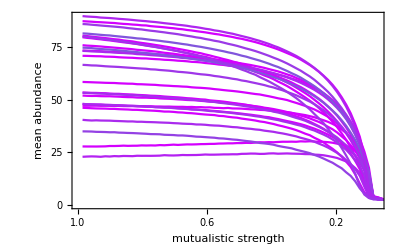
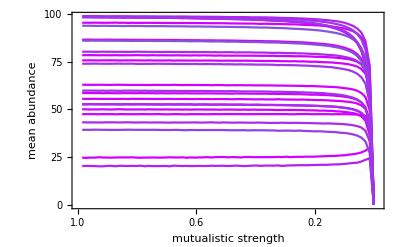

```mathematica
network = 6;
SensorScore=SS⟦network⟧;
vertexColors=(Blend[{ RGBColor[0.8300000000000001, 0, 1],RGBColor[0, 0.85, 0.65]},Rescale[#,{0,1}]]&)[#]&/@SensorScore;
meanpl=Table[
ListPlot[m11⟦i⟧,
Joined->True,
Frame->True,
PlotStyle->Partition[vertexColors,1],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
PlotRange->{{0,maxdie⟦i⟧+2},Automatic},
FrameTicksStyle->11,
FrameTicks->{{Range[0,100,25],None} ,{TicksL,None}},
FrameLabel->{"mutualistic strength","mean abundance",""}
],{i,{1,3,5}}]
```

### variance change

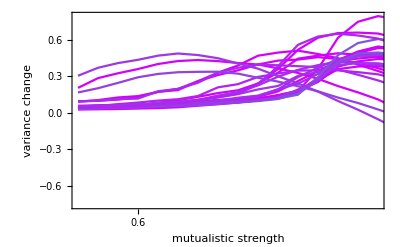
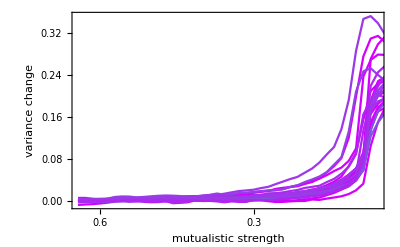
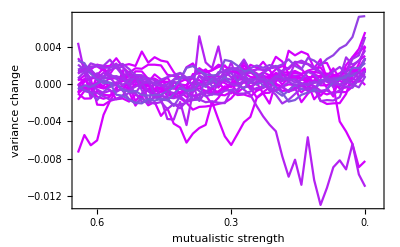

```mathematica
mu11 =N[Range[1,0,-1/Length[Transpose[m113]]]⟦-Length[Transpose[vch113]];;-1⟧];
1-(maxdie⟦1⟧+2)/70;
datCh = Table[Table[Transpose@{mu11,v11⟦i⟧⟦j⟧},{j,Length@v11⟦1⟧}],{i,5}];
vchpl=Table[ListPlot[datCh⟦i⟧,
Joined->True,
Frame->True,
PlotStyle->Partition[vertexColors,1],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
PlotRange->{{Max@mu2,1-(maxdie⟦i⟧+2)/70},Full},
PlotRange->Full,
FrameTicksStyle->11,
FrameTicks->{Automatic ,{Range[0,1,0.15],None}},
FrameLabel->{"mutualistic strength","variance change",""},
ScalingFunctions->{"Reverse",None}
],{i,{1,3,5}}]
```

### Sensor score vs early - warning score

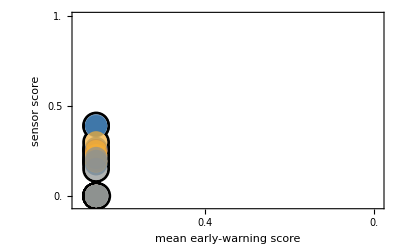
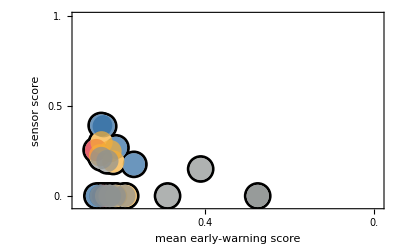
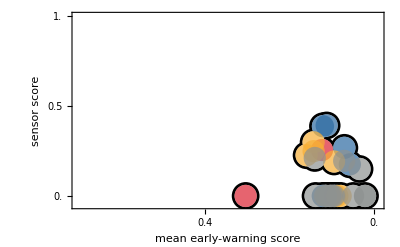

```mathematica
network = 6;

figs2=Table[

SensorScore = SS⟦network⟧;
vertexDegree=Deg⟦network⟧;
medianEW = ews⟦repetition⟧//Flatten;

n = Length@SensorScore;

degrees = Sort@DeleteDuplicates@vertexDegree;
deg = degrees⟦1⟧;

temp=Table[
pos = Position[vertexDegree,deg]//Flatten;

ListPlot[Thread[{medianEW⟦pos⟧, SensorScore⟦pos⟧}],
PlotRange->{{0-0.01,Max@medianEW+0.01},{-0.05,1}},
GridLines->{{},{Max@SensorScore}},
GridLinesStyle->Directive[Gray,Dashed],
PlotStyle->Directive[GetColor[deg], PointSize[0.04],Opacity[0.7]],
 FrameTicks->{{Range[0,1,0.2],None},{Range[0,Max@medianEW,0.05],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True
]
,{deg,degrees}];

temp2 = ListPlot[Thread[{medianEW, SensorScore}],
PlotRange->{{0-0.01,0.7},{-0.05,1}},
(*GridLines->{{},{Max@SensorScore}},*)
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,120},
FrameTicks->{{Range[0,1,0.5],None},{Range[0,1,0.2],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True,
PlotStyle-> Directive[Black, PointSize[0.05],Opacity[1]],
FrameTicksStyle->11,
FrameLabel->{"mean early-warning score","sensor score",""}
];

temp3 = ListPlot[Thread[{medianEW, SensorScore}],
ScalingFunctions->{"Reverse",Identity},
PlotStyle-> Directive[White, PointSize[0.04],Opacity[1]]
];

Show[temp2,temp3,temp,
FrameTicksStyle->11
]
,{repetition,Range[3]}]
```